# Exploring the DNN Model of the d^4 σ^UU Observable:

## (#0): Initializing Cells:

## (#0.1): Glorot Uniform Distribution:

```mathematica
glorotNormalMatrix[previousLayerDimension_,finalLayerDimension_]:=
RandomVariate[
NormalDistribution[0,√(2/(previousLayerDimension + finalLayerDimension))], (* zero mean and some specific spread--look online for "Xavier Normal"*)
{finalLayerDimension,previousLayerDimension}
]
```

```mathematica
glorotNormalMatrix[2,4]//MatrixForm
```

## (#1): Analytical DNN Model:

## (#1.1): Definition of the analytical model:

Recall that the features are t, x_B, Q^2, and ϕ and the single label is the d^4 σ^UU:
1. Activation functions are ReLU
2. Hidden layers are initialized by GlorotUniform

```mathematica
CrossSectionSurrogateDNNModel[t_,xb_,qsq_,ϕ_]=
glorotNormalMatrix[16,1].
Ramp[
(* preactivations layer 3 *)
glorotNormalMatrix[16,16].
Ramp[
(* preactivations layer 2 *)
glorotNormalMatrix[16,16].
Ramp[
(* preactivaitons layer 1 *)
glorotNormalMatrix[4,16].
(* feature vector *)
{t,xb,qsq,ϕ}
]
]
];
```

## (#1.2): Evaluating the untrained model for some random values of t, x_B, Q^2, and ϕ:

```mathematica
CrossSectionSurrogateDNNModel[-0.1337, 0.1342, 1.1661,2.792077]
```

## (#1.A): Gradient Descent Analysis:

Just checking some stuff...

```mathematica
(* DO NOT TAKE THIS DERIVATIVE ANYMORE *)
(*D[CrossSectionSurrogateDNNModel[t,xb,qsq,ϕ],t]*)
```

## (#1.B): Plots of the analytical model:

The main thing we want to check here is that untrained weights do not lead to miraculous fits!

```mathematica
Plot[CrossSectionSurrogateDNNModel[-0.5,0.2,2.4,ϕ],{ϕ,0,2π}]
```

### (#1.B.1): Untrained model surface across t and ϕ:

```mathematica
(* Fixing Subscript[x, B] and Q^2 here! *)
Plot3D[
CrossSectionSurrogateDNNModel[t,0.2,2.4,ϕ],{ϕ,0,2π},{t,-1.0,-0.1},
PlotLabel->"d^4σ^UU Surrogate DNN Foliataion Across ϕ and t",
AxesLabel->{"ϕ (radians)","t (GeV^2)","DNN Evaluation"}]
```

### (#1.B.2): Untrained model surface across x_B and ϕ:

```mathematica
(* Fixing t and Q^2 here! *)
Plot3D[
CrossSectionSurrogateDNNModel[-0.5,xb,2.4,ϕ],{ϕ,0,2π},{xb,0.01,1.0},
PlotLabel->"d^4σ^UU Surrogate DNN Foliataion Across ϕ and x_B",
AxesLabel->{"ϕ (radians)","x_B","DNN Evaluation"}]
```

### (#1.B.3): Untrained model surface across Q^2 and ϕ:

```mathematica
(* Fixing t and Subscript[x, B] here! *)
Plot3D[
CrossSectionSurrogateDNNModel[-0.5,0.3,qsq,ϕ],{ϕ,0,2π},{qsq,1.0,7.0},
PlotLabel->"d^4σ^UU  Surrogate DNN Foliataion Across ϕ and x_B",
AxesLabel->{"ϕ (radians)","Q^2 (GeV^2)","DNN Evaluation"}]
```

## (#2): Data Loading and Preprocessing:

## (#2.1): Loading in the Dataset:

### (#2.1.1): Actually loading the dataset:

```mathematica
dataset=Import["DIRECTORIES!",
"Dataset",
(* https://mathematica.stackexchange.com/a/202094 -> for what the point of "HeaderLines" is, and how to query sub-datasets *)
"HeaderLines"->1
];
```

### (#2.1.2): How to query a sub-dataset using logical operations:

```mathematica
(* the set 324 actually exists, and that's why we use this to test out the sub-dataframe construction *)
dataset[Select[#["set"]==324&]]
```

## (#2.2): Defining the Features/Labels:

### (#2.2.1): Defining the strings for the features and the labels:

```mathematica
featureColumns={"k", "t","x_b","q_squared","phi"};
labelColumn="unp_beam_unp_target_xsec";
```

### (#2.2.2): Data preprocessing:

#### (#2.2.2.1): Obtain the raw data:

```mathematica
rawFeatures=Values[Normal[dataset[All,featureColumns]]];
rawLabels=List/@Normal[dataset[All,labelColumn]];
```

#### (#2.2.2.2): Standardization, column-wise:

```mathematica
standardizedFeatures=Standardize[rawFeatures];
standardizedLabels=List/@Standardize[Flatten[rawLabels]];
```

After standardization, the distribution of data should be 𝒩(0, 1). Let’s check it:

```mathematica
Mean[standardizedFeatures]
StandardDeviation[standardizedFeatures]
```

Close enough!

#### (#2.2.2.3): Compute pre-standardized statistics:

```mathematica
(* FYI: super jank feature where Max/Min are global (flattening) functions and Mean/SD is vectorized already... WOW! *)
(* All of that is to say that the following code below does NOT return what we want: *)
(* 
featureMinimums=Min[rawFeatures];
featureMaximums=Max[rawFeatures];
labelMinimums=Min[rawLabels];
labelMaximums=Max[rawLabels];
*)
```

```mathematica
featureMinimums=Min/@Transpose[rawFeatures]
featureMaximums=Max/@Transpose[rawFeatures]
labelMinimums=Min/@Transpose[rawLabels]
labelMaximums=Max/@Transpose[rawLabels]
```

```mathematica
featureMeans=Mean[rawFeatures];
featureSDs=StandardDeviation[rawFeatures];
labelMeans=Mean[Flatten[rawLabels]];
labelSDs=StandardDeviation[Flatten[rawLabels]];
```

What are the minimums?

```mathematica
featureMinimums
labelMinimums
```

```mathematica
featureMaximums
labelMaximums
```

Let’s look at the means of each feature:

```mathematica
featureMeans
```

Let’s look at the SDs:

```mathematica
featureSDs
```

#### (#2.2.2.4): Forward-standardization function (explicitly written):

```mathematica
forwardStandardizeFeatures[rawTuple_List]:=(rawTuple-featureMeans)/featureSDs
forwardStandardizeLabels[rawTuple_List]:=(rawTuple-labelMeans)/labelSDs
```

Let’s test this momentarily:

```mathematica
forwardStandardizeFeatures[{5.75,-0.1337,0.1342,1.661,0}]
```

#### (#2.2.2.5): Inverse-standardization function (explicitly written):

```mathematica
inverseStandardizeFeatures[scaledOutput_]:=(scaledOutput * featureSDs)+featureMeans
inverseStandardizeLabel[scaledOutput_]:=(scaledOutput * labelSDs)+labelMeans
```

Should be able to reverse the previous operation:

```mathematica
inverseStandardizeFeatures[forwardStandardizeFeatures[{5.75,-0.1337,0.1342,1.661,0}]]
```

Excellent!

### (#2.2.2): Actually generating the Dataset:

```mathematica
(*
features=Values[Normal[dataset[All,featureColumns]]];
labels=List/@Normal[dataset[All,labelColumn]];
(* this is a Mathematica "association" structure: *)
labeledData=<|"Input"->features,"Output"->labels|>;
*)
```

```mathematica
(*
features=Values[Normal[dataset[All,standardizedFeatures]]];
labels=List/@Normal[dataset[All,standardizedLabels]];
*)
labeledData=<|"Input"->standardizedFeatures,"Output"->standardizedLabels|>;
```

## (#3): Actual DNN Model:

## (#3.1): Defining the NetChain[] Model:

### (#3.1.1): Initializing the Surrogate Model:

```mathematica
CrossSectionSurrogateModel=NetChain[
{
LinearLayer[64],Ramp,
LinearLayer[64],Ramp,
LinearLayer[64],Ramp,
LinearLayer[1]
},
"Input"->5,
"Output"->1]
```

### (#3.1.2): Some fun graphic for the model flow:

```mathematica
(* this line is actually from: https://www.wolfram.com/language/introduction-machine-learning/regression/ *)
Information[CrossSectionSurrogateModel,"SummaryGraphic"]
```

### (#3.1.3): Initializing the model:

```mathematica
initializedCrossSectionSurrogateModel=NetInitialize[CrossSectionSurrogateModel]
```

## (#3.2): DNN Training Happens Here!

```mathematica
(* https://mathematica.stackexchange.com/q/164470 -> for ADAM optimizer parameters *)
	trainedModel=NetTrain[
	initializedCrossSectionSurrogateModel,
	labeledData,
	(* this randomly samples 20% of the training data---it is smart enough to know how to do that*)
	ValidationSet->Scaled[0.2],
	Method->{
	"ADAM"
	(* LearningRate->0.001, *)
	(* "Beta1"->0.9, (* default setting! *) *)
	(* "Beta2"->0.999, (* default setting! *) *)
	(* "Epsilon"-> Rational[1,100000] *)
	},
	MaxTrainingRounds->1500,
	BatchSize->8
	]
```

## (#3.3): Let’s get comfortable making predictions:

[NOTE]: Remember the order of the inputs: the data was read in as: “t”, “x_b”, “q_squared”, “phi”.

### (#3.3.1): Making some joke predictions:

```mathematica
forwardStandardizeFeatures[{5.75,-0.1337,0.1342,1.661,0}]
```

```mathematica
{
trainedModel[forwardStandardizeFeatures[{5.75,-0.1337,0.1342,1.661,0}]],
trainedModel[forwardStandardizeFeatures[{5.75,-0.1337,0.1342,1.661,π/2}]],
trainedModel[forwardStandardizeFeatures[{5.75,-0.1337,0.1342,1.661,π}]],
trainedModel[forwardStandardizeFeatures[{5.75,-0.1337,0.1342,1.661,(3π)/2}]],
trainedModel[forwardStandardizeFeatures[{5.75,-0.1337,0.1342,1.661,2π}]]
}
```

The output is the standardized features:

```mathematica
inverseStandardizeLabel[{{3.9542348384857178},{14.81836986541748},{32.76520919799805},{48.77935791015625},{61.44507598876953}}]
```

And these values should be in nb/GeV^4.

### (#3.3.2): What are the values for -π and π?

```mathematica
forwardStandardizeFeatures[{5.75,-0.1337,0.1342,1.661,-π}]
forwardStandardizeFeatures[{5.75,-0.1337,0.1342,1.661,π}]
```

## (#4): DNN Model Predictions:

## (#4.1): Plot a single local prediction:

### (#4.1.1): Making DNN Predictions at Fixed Kinematics present in the original dataset vs. ϕ:

Make sure you understand the syntax below, particularly why we can use the index [[1]]. (Also understand why we can use the magic number 324

```mathematica
localFitBin1FixedK=dataset[Select[#["set"]==324&]][[1]]["k"];
localFitBin1FixedT=dataset[Select[#["set"]==324&]][[1]]["t"];
localFitBin1FixedXBjorken=dataset[Select[#["set"]==324&]][[1]]["x_b"];
localFitBin1FixedQSquared=dataset[Select[#["set"]==324&]][[1]]["q_squared"];
```

The cell below is also quite complicated; it took me a while to figure out what is going on, but it works. The idea is, to plot the actual datapoints, we need to make a list of lists: a list of the “tuples” of the ϕ and BSA. So, we did that using a series of sub-dataset constructions and datatype manipulations:

```mathematica
localFitBin1PhiAndCrossSection=Values[Normal[dataset[Select[#["set"]==324&],{"phi","unp_beam_unp_target_xsec"}]]];
```

[NOTE]: What is the output of the DNN? Is it a scalar, or a list with one scalar?

```mathematica
localFitBin1PhiAndCrossSection
```

### (#4.1.2): Show the corresponding local fit plot:

```mathematica
Show[
Plot[
First[
trainedModel[
forwardStandardizeFeatures[{localFitBin1FixedK,localFitBin1FixedT,localFitBin1FixedXBjorken,localFitBin1FixedQSquared,phi}]
]],{phi,-1.764786363823739,1.764786363823739},
PlotStyle->Directive[Thick,Blue],
PlotLegends->{"DNN Predictions"}
],
ListPlot[
localFitBin1PhiAndCrossSection,
PlotStyle->Directive[Red,PointSize[Medium]],
PlotLegends->{"Experimental Data (Set 1)"}
],
AxesLabel->{"ϕ (radians)", "d^4σ^UU (nb/GeV^-4"},
PlotLabel->StringForm["Surrogate DNN Local Fit at k = `1`, t = `2`, x_B = `3`, Q.b2 = `4`",localFitBin1FixedK, localFitBin1FixedT,localFitBin1FixedXBjorken,localFitBin1FixedQSquared],
GridLines->Automatic,
PlotRange->All
]
```

## (#4.2): Making several plots of all possible local predictions:

### (#4.2.1): Grouping the Dataset by unique kinematic settings, (k, t, x_B, Q^2):

```mathematica
groupedKinematicSettingsDataset=Values[GroupBy[dataset,{#["k"],#["t"],#["x_b"],#["q_squared"]}&]]//Normal;
```

### (#4.2.2): A huge module that basically runs the local fitting plot logic we already coded above:

```mathematica
makeKinematicPlot[subGroup_]:=Module[{firstRow,fixedK, fixedT,fixedXb,fixedQ2,phiAndBsa},

firstRow=subGroup[[1]];
fixedK=firstRow["k"];
fixedT=firstRow["t"];
fixedXb=firstRow["x_b"];
fixedQ2=firstRow["q_squared"];

phiAndBsa=Lookup[subGroup,{"phi","unp_beam_unp_target_xsec"}];

Show[
Plot[
First[trainedModel[{fixedK,fixedT,fixedXb,fixedQ2,phi}]],{phi,-π,π},
PlotStyle->Directive[Thick,Blue],
PlotLegends->{"DNN Predictions"}
],
ListPlot[
phiAndBsa,
PlotStyle->Directive[Red,PointSize[Medium]],
PlotLegends->{"Experimental Data"}
],
AxesLabel->{"ϕ (radians)", "d^4σ^UU (nb/GeV^-4"},
PlotLabel->StringForm["Surrogate DNN Fit at k = `1`, t = `2`, x_B = `3`, Q.b2 = `4`",localFitBin1FixedK, localFitBin1FixedT,localFitBin1FixedXBjorken,localFitBin1FixedQSquared],
GridLines->Automatic,PlotRange->All]
]
```

### (#4.2.3): Run the module across all of the bins in the kinematic settings dataset:

```mathematica
(* below is essentially list comprehension, i.e. that's how we should read it *)
allPlots=Table[makeKinematicPlot[kinematicBin],{kinematicBin,groupedKinematicSettingsDataset}];
```

### (#4.2.4): [DANGER!]: This will make a Nx3 Grid of Local Fit Plots! THIS CAN AND MIGHT CRASH YOUR NOTEBOOK. WE WILL PROBABLY CHANGE THIS LATER---IT IS TEMPORARY RIGHT NOW.

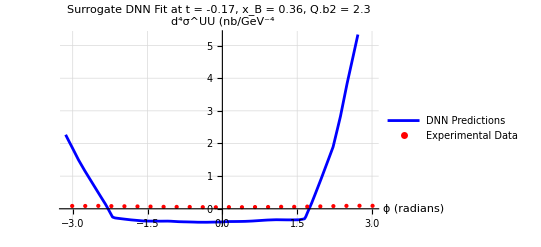
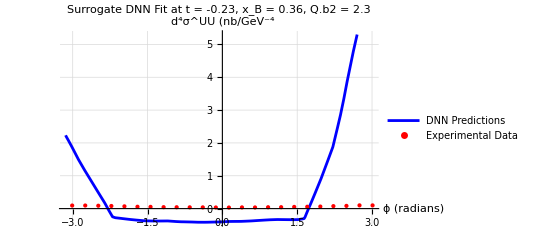
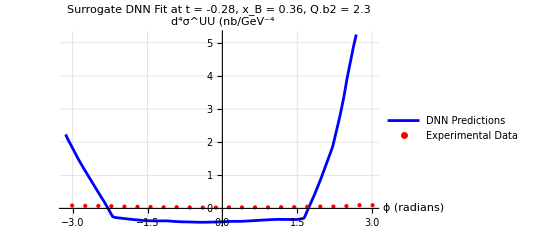
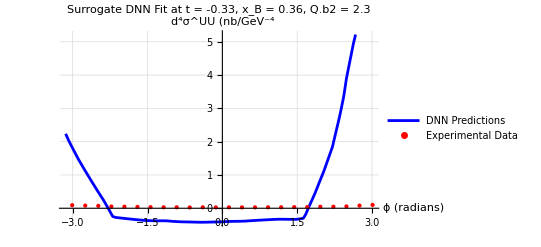
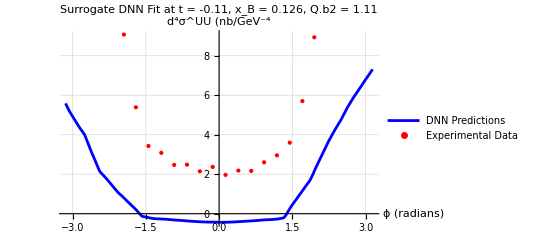
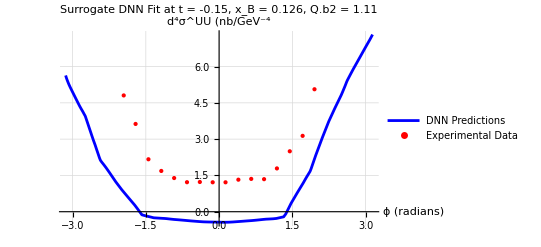
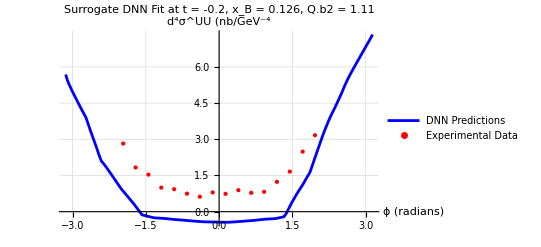
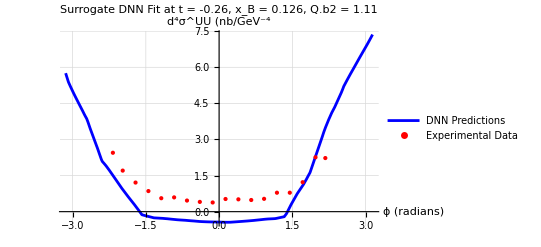
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
Partition[allPlots,2]//Grid
```

## (#Z): Figuring Stuff Out: